```mathematica
ClearAll["Global`*"];
(*Rakieta, której masa początkowa wynosi m, startuje pionowo do góry. Znaleźć przyspieszenie,z jakim porusza się rakieta po czasie t=5 s
od chwili startu, jeżeli szybkość spalania paliwa rakiety µ=0,1 kg/s, a
względna szybkość wylatujących produktów spalania wynosi v. Sporządzić
wykresy dla v=100÷150 m/s w dwóch przypadkach:
a) m=1 kg, b) m=1.5 kg.*)
```

```mathematica
t=5;             (* s *)
```

```mathematica
μ=0.1;       (* kg/s *)
```

```mathematica
g=9.81;     (* m/s^2 *)
```

```mathematica
ms=μ×t;
```

```mathematica
Fg=(m-ms)×g;
```

```mathematica
Fc=μ×v;
```

```mathematica
A=Solve[ (m-ms)×a==Fc-Fg,a]
```

{{a→(-9.81 (-0.5+m)+0.1 v)/(-0.5+m)}}

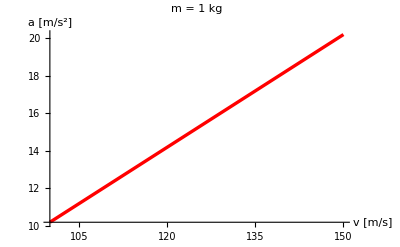

```mathematica
rys1=Plot[a/.A/.m->1,{v,100,150},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     m = 1 kg  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v [m/s]","a [m/s^2] "}]
```

### Sporzadzenie wykresu obrazujacego zaleznosc przyspieszenia rakiety od szybkosci wylatujacych spalin dla poczatkowej masy rakiety rownej 1.5 kg.

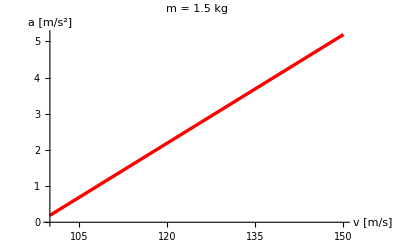

```mathematica
rys1=Plot[a/.A/.m->1.5,{v,100,150},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     m = 1.5 kg  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v [m/s]","a [m/s^2] "}]
```